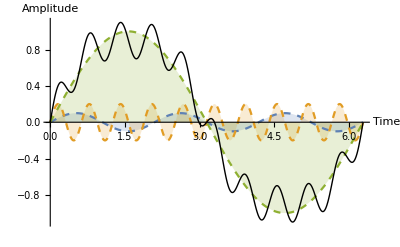

```mathematica
a[x_] := 0.1Sin[3x]
b[x_] := 0.2Sin[10x]
c[x_] := Sin[1x]
Show[{Plot[{a[x],b[x],c[x]},{x,0,2  Pi}, AxesLabel->{"Time", "Amplitude"},Filling->Axis, PlotStyle->{Dashed}],
Plot[a[x] + b[x] + c[x], {x, 0, 2Pi}, PlotStyle->{Black, Thick}] 
}, PlotRange->All
	]
```

```mathematica
Export[ "/tmp/sinewaves.pdf", Out[170]]
```

/tmp/sinewaves.pdf

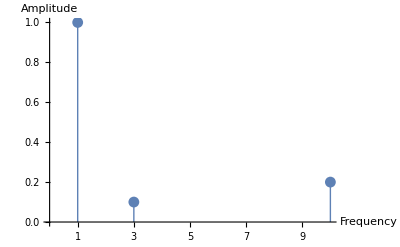

```mathematica
ListPlot[{{1, 1}, {3, 0.1}, {10,0.2}}, Filling->Axis,Ticks->{{1, 2, 3, 4, 5,6, 7, 8, 9, 10}, Automatic},AxesLabel->{"Frequency", "Amplitude"},  FillingStyle->{Black, Thick}]
```

```mathematica
Export["/tmp/partials.pdf", Out[139]]
```

/tmp/partials.pdf

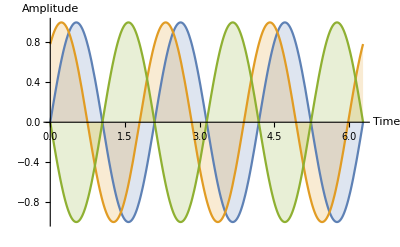

```mathematica
a[x_] := Sin[3x]
b[x_] := Sin[3x +0.9]
c[x_] := -Sin[3x]
Show[{Plot[{a[x],b[x],c[x]},{x,0,2  Pi}, AxesLabel->{"Time", "Amplitude"},Filling->Axis]}, PlotRange->All
	]
```

```mathematica
Export["/tmp/phases.pdf",  Out[165]]
```

/tmp/phases.pdf

```mathematica
2^14.428491035332245
```

22050.